## What does the mean first passage time look like with viscosity?

```mathematica
params={R->.25,θ->Pi/8,kBT->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"],"Piconewtons"*"Micrometers"]],v->1}
```

{R→0.25,θ→π/8,kBT→0.00414195,v→1}

```mathematica
rotationalMFP[η_]:=R^2/(kBT/(8 Pi η R^3)) Log[(1-Cos[Pi])/(1-Cos[θ])]
```

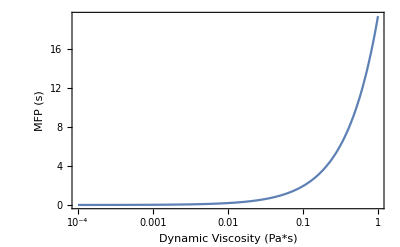

```mathematica
LogLinearPlot[rotationalMFP[η]/.params,{η,1*^-4,1},Frame->True,FrameLabel->{"Dynamic Viscosity (Pa*s)","MFP (s)"},PlotRange->All]
```

Water has a dynamic viscosity of

```mathematica
ChemicalData["Water","Viscosity"]
```

0.00089 s Pa

## How high does it need to be to pose a serious impediment to the motors?

```mathematica
drag[η_]:=8Pi η R v
```

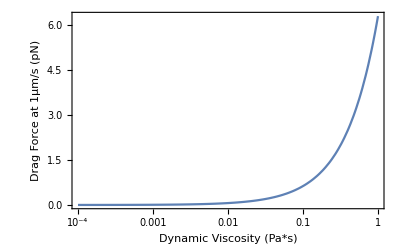

```mathematica
LogLinearPlot[drag[η]/.params,{η,1*^-4,1},Frame->True,FrameLabel->{"Dynamic Viscosity (Pa*s)","Drag Force at 1μm/s (pN)"},PlotRange->All]
```

So for drag forces to be significant, the MFP for even small cargos is > 10 seconds